```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* odd even 6star 6 cycle *)
```

```mathematica
n0=6
```

6

```mathematica
(* substitution *)
```

```mathematica
s[1]={3,5,6,0,0,0,0,0}; s[2]={4,6,3,0,0,0,0,0}; s[3]={1,5,2,0,0,0,0,0}; s[4]={2,6,5,0,0,0,0,0,0};s[5]={1,3,4,0,0,0,0,0,0};
s[6]={2,4,1,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{0,0,1,0,1,1},{0,0,1,1,0,1},{1,1,0,0,1,0},{0,1,0,0,1,1},{1,0,1,1,0,0},{1,1,0,1,0,0}}

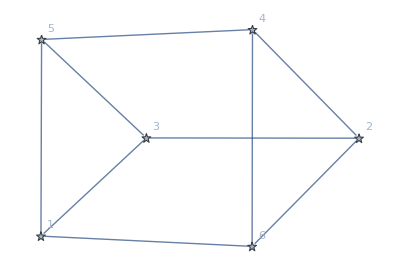

```mathematica
AdjacencyGraph[M,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

12 x^2-4 x^3-9 x^4+x^6

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x]
```

{-2.,-2.,0.,0.,1.,3.}

```mathematica
Abs[%]
```

{2.,2.,0.,0.,1.,3.}

```mathematica
Clear[s,p]
```

```mathematica
(* program to express the substitution *)
```

```mathematica
Clear[s,t,p]
```

```mathematica
s[1]={3,5,6}; s[2]={4,6,3}; s[3]={1,5,2}; s[4]={2,6,5};s[5]={1,3,4};
s[6]={2,4,1};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Join[Flatten[Table[s[i],{i,6}]],Reverse[Flatten[Table[s[i],{i,6}]]]]
```

{3,5,6,4,6,3,1,5,2,2,6,5,1,3,4,2,4,1,1,4,2,4,3,1,5,6,2,2,5,1,3,6,4,6,5,3}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[9];
```

```mathematica
Length[aa]
```

708588

```mathematica
(* graphing subroutine*)
```

```mathematica
v=Table[N[{Cos[2*Pi*i/6],Sin[2*Pi*i/6]}],{i,6}]
```

{{0.5,0.866025},{-0.5,0.866025},{-1.,0.},{-0.5,-0.866025},{0.5,-0.866025},{1.,0.}}

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]]/. 6->v[[6]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,PlotRange->All,Axes->False,ImageSize->{2000,2000},PlotStyle->{PointSize[0.001]},ColorFunction->Hue];
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","ManganeseBlue","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
dd=Flatten[ParallelTable[{PointSize[0.001],cols[[aa[[n]]]],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g1=Show[Graphics[dd],ImageSize->{2000,2000}];
```

```mathematica
Export["6Symbol_odd_even_cycle6_Hexagon_level9_doubleStartvector.jpg",GraphicsGrid[{{g0},{g1}},ImageSize->{2000,4000}]]
```

6Symbol_odd_even_cycle6_Hexagon_level9_doubleStartvector.jpg

```mathematica
(*end*)
```